# Computation

## Basic primitives, Rules for evolutions,

```mathematica
f[#, a, #, b]&[x, y]
```

f[x,a,x,b]

```mathematica
D[f[x,a,x,b], x]
```

f^(0,0,1,0)[x,a,x,b]+f^(1,0,0,0)[x,a,x,b]

```mathematica
f[#1,#2, #1, #3]&[x, y, z]
```

f[x,y,x,z]

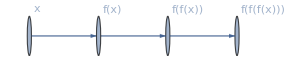

```mathematica
NestGraph[f, x, 3, VertexLabels->Automatic]
```

```mathematica
{3, 5, 1}
```

{3,5,1}

```mathematica
%
```

{3,5,1}

```mathematica
Exp[%]//N
```

{20.0855,148.413,2.71828}

```mathematica
Table[i^2, {i, 8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
Norm[{1,4,9,16,25,36,49,64},2]
```

2 √2193

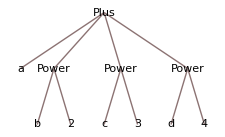

```mathematica
TreeForm[a + b^2+c^3 + d^4]
```

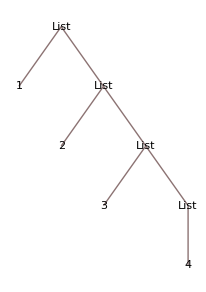

```mathematica
TreeForm[{1, {2, {3, {4}}}}]
```

```mathematica
#2 &[1, 2, 3, 5]
```

2

```mathematica
#x&[<|"x" -> a, "y" -> b|>]
```

a

```mathematica
f[#u, #v, #x, #u]&[<|"u"-> z, "v" -> y, "x" -> z|>]
```

f[z,y,z,z]

```mathematica
tensor=ResourceFunction["AdjacencyTensor"][{{1,2},{1,3},{2,3},{2,4},{3,4}}]
```

SparseArray[…]

```mathematica
<|a -> x, b -> y, c -> z|>
```

<|a→x,b→y,c→z|>

```mathematica
<|a->x,b->y,c->z|>[a]
```

x

```mathematica
Function[{u, v}, u^2+ v^4][x, y]
```

x^2+y^4

```mathematica
f[##]&[a, b, c, d]
```

f[a,b,c,d]

```mathematica
{x, x^2, a, b, c}/. x-> 4
```

{4,16,a,b,c}

```mathematica
{x, x, x^5, x} /.x -> 2.023
```

{2.023,2.023,33.8828,2.023}

```mathematica
ListPlot3D[Table[Sin[j^3+ i], {i, 0, 2Pi, 0.1}, {j, 0, 2Pi, 0.1}]]
```

-Graphics3D-

```mathematica
Table[BernoulliB[n], {n, 0, 15}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66,0,-691/2730,0,7/6,0}

```mathematica
∫_0^∞ Sinh[x/2]/xCosh[x] ⅆx
```

∫_0^∞ Sinh[x/2]/xCosh[x]ⅆx

```mathematica
Zeta[-1]
```

-1/12

```mathematica
Zeta[2]
```

π^2/6

```mathematica
pol = Polygon[{{1, 0, 0}, {1, 1, 1}, {0, 0, 1}}]
```

Polygon[…]

```mathematica
RegionCentroid[pol]
```

{1-1/3 √(2/3) (√(2/3)+1/(√6)),(1/(√2)+√2)/(3 √2)-(√(2/3)+1/(√6))/(3 √6),(1/(√2)+√2)/(3 √2)+(√(2/3)+1/(√6))/(3 √6)}

```mathematica
Region[pol]
```

-Graphics3D-

```mathematica
RegionPlot[pol]
```

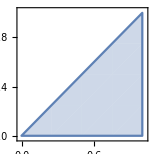

```mathematica
ResourceFunction["AbstractCategory"]
```

```mathematica
category2=[category,{},category["CommutativityEquations"]]
```

FunctionRepository`$950b51fffc014fa1a5d9cef28232e972`AbstractCategory[category,{},category[CommutativityEquations]]

```mathematica
Table[i^2, {i, 14}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196}

```mathematica
Table[x, 12]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Partition[{x,x,x,x,x,x,x,x,x,x},4]
```

{{x,x,x,x},{x,x,x,x}}

```mathematica
Style[Row[{2,2,3,2,3,2,2,2,2}/. {2->Style[2,RGBColor[0.91, 0.16379999999999995, 0., 1]],3->Style[3,RGBColor[0.6, 0.17, 0.85]]}][1]==Row[{3,3,3,3,2,3,3}/. {2->Style[2,RGBColor[0.91, 0.16379999999999995, 0., 1]],3->Style[3,RGBColor[0.56, 0.39100000000000024, 0.85]]}][1],17,FontFamily->"Times"]
```

223232222[1]==3333233[1]

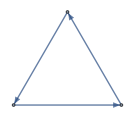

```mathematica
Graph[{1 -> 2, 2 -> 3, 3-> 1}]
```

```mathematica
KirchhoffMatrix[Graph[{1, 2, 3}, {DirectedEdge[1, 2], DirectedEdge[2, 3], DirectedEdge[3, 1]}]]
```

SparseArray[…]

```mathematica
g = -Graphics-
```

-Graphics-

```mathematica
FindShortestPath[g,3,6]
```

{3,1,6}

```mathematica
Graph3D[ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n↦{If[IntegerQ[#],#,None]&[2n],If[IntegerQ[#],#,None]&[(n-1)/3]},{1},32],All]]
```

-Graphics3D-

```mathematica
Table[10i + j, {i, 5}, {j, 4}]
```

{{11,12,13,14},{21,22,23,24},{31,32,33,34},{41,42,43,44},{51,52,53,54}}

```mathematica
Grid[{{11,12,13,14},{21,22,23,24},{31,32,33,34},{41,42,43,44},{51,52,53,54}}]
```

11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34
41 | 42 | 43 | 44
51 | 52 | 53 | 54

```mathematica
DiagonalMatrix[{a, b,c}]//MatrixForm
```

(a | 0 | 0
0 | b | 0
0 | 0 | c)

```mathematica
Inverse[{{a,0,0},{0,b,0},{0,0,c}}]
```

{{1/a,0,0},{0,1/b,0},{0,0,1/c}}

```mathematica
x^2  - 1
```

-1+x^2

```mathematica
PolyhedronData["Icosahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["MathematicaPolyhedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

## Turing Machines RulePlot

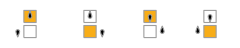

```mathematica
RulePlot[TuringMachine[2506]]
```

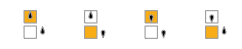

```mathematica
RulePlot[TuringMachine[1003]]
```

```mathematica
RulePlot[TuringMachine[2506],{{1,6},Table[0,10]},25,Mesh->True,Frame->False]
```

-Graphics-

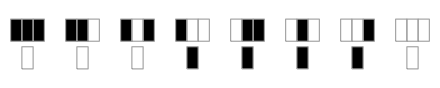

```mathematica
RulePlot[CellularAutomaton[30]]
```

```mathematica
RandomImage[]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[30], {{1}, 0}, 100]
```

-Graphics-

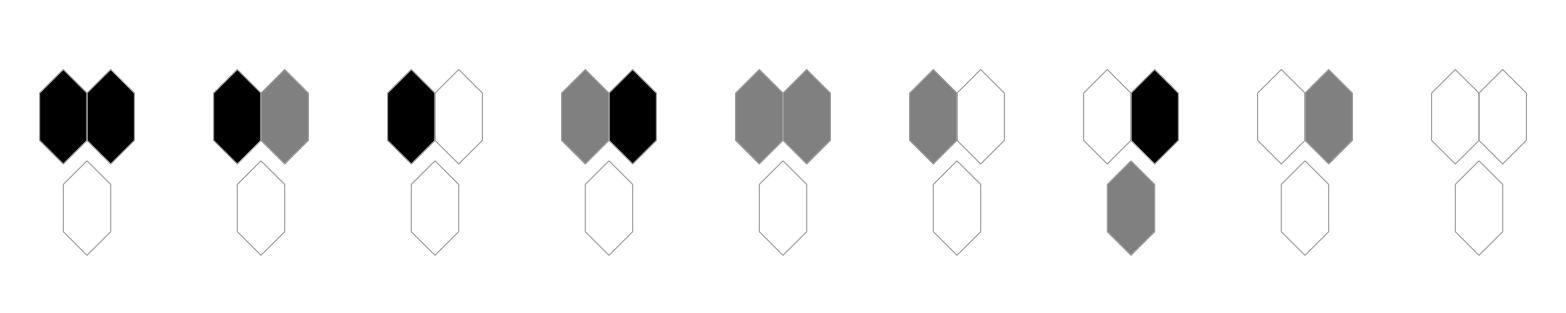

```mathematica
RulePlot[CellularAutomaton[{9,3,1/2}],Appearance->"Hexagons"]
```

```mathematica
RandomPolygon[]
```

Polygon[…]

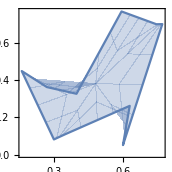

```mathematica
RegionPlot[%23]
```

```mathematica
RegionCentroid[%23]
```

{0.512181,0.401211}

## Turing Machines

## MultiwayTuringMachines

```mathematica
CloudGet["https://www.wolframcloud.com/obj/sw-blog/MultiwayTuringMachines/Programs-01.wl"];With[{t=3},MultiwayTuringMachine[{{{1,1}->{2,0,-1}},{{1,0}->{2,1,1}},{{1,0}->{2,0,-1}},{{2,1}->{1,0,1}},{{2,0}->{1,1,-1}}},{{1,t+1},Table[0,2 t+1]},t,"StatesGraph",VertexSize->.8 {1,.2},GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[%27]
```

SparseArray[…]

## Chemistry

```mathematica
Entity["Chemical","Oxytocin"]
```

oxytocin

```mathematica
ChemicalData[Entity["Chemical","Oxytocin"],"IsomericSMILES"]
```

CC[C@H](C)[C@@H]1NC(=O)[C@H](CC2=CC=C(O)C=C2)NC(=O)[C@@H](N)CSSC[C@H](NC(=O)[C@H](CC(N)=O)NC(=O)[C@H](CCC(N)=O)NC1=O)C(=O)N1CCC[C@H]1C(=O)N[C@@H](CC(C)C)C(=O)NCC(N)=O

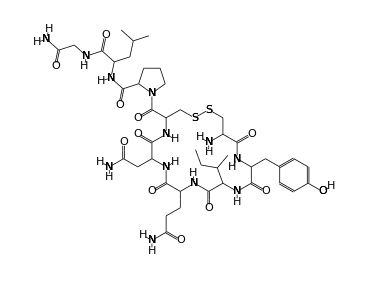

```mathematica
ChemicalData[Entity["Chemical","Oxytocin"],"StructureDiagram"]
```

```mathematica
CommonName[Entity["Chemical","Oxytocin"]]
```

oxytocin

```mathematica
PhysicalSystemData["SampleEntities"]
```

{charged sphere,circular current loop,double pendulum,free particle in 1D,harmonic oscillator,ideal gas,inverse-distance potential in 3D in spherical coordinates,particle in a box in 1D,pendulum,point mass,rectangular bar magnet,van der Waals gas}

-Graphics-

## Computation

### Graphs

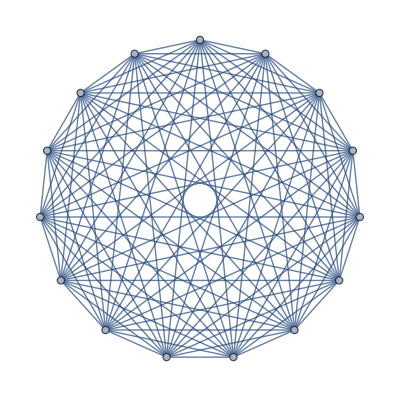

```mathematica
GraphPlot[ConstantArray[1, {15, 15}]]
```

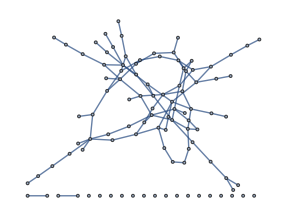

```mathematica
GraphPlot[RandomChoice[{0.01, 0.9} -> {1, 0}, {100, 100}]]
```

## Linguistics

```mathematica
words_sion = DictionaryLookup["*sion"]
```

{abrasion,abscission,accession,adhesion,admission,aggression,allusion,animadversion,antidiffusion,apprehension,ascension,Ascension,aspersion,aversion,cession,circumcision,cohesion,collision,collusion,commission,compassion,comprehension,compression,compulsion,concession,concision,conclusion,concussion,condescension,confession,confusion,contusion,conversion,convulsion,corrosion,decision,declension,decommission,decompression,delusion,depression,derision,diffusion,digression,dimension,discussion,disillusion,dispassion,dispersion,dispossession,dissension,dissuasion,distension,diversion,division,effusion,elision,emission,emulsion,envision,erosion,evasion,excision,exclusion,excursion,expansion,explosion,expression,expulsion,extension,extroversion,extrusion,fission,fusion,hypertension,illusion,immersion,implosion,imprecision,impression,impulsion,incision,inclusion,incomprehension,incursion,indecision,infusion,ingression,intercession,interconversion,intermission,intersession,interspersion,introversion,intrusion,invasion,inversion,lesion,malocclusion,mansion,manumission,misapprehension,misprision,mission,nonaggression,obsession,obtrusion,occasion,occlusion,omission,oppression,passion,Passion,pension,percussion,perfusion,permission,persuasion,perversion,possession,precession,precision,preclusion,prepossession,pretension,prevision,procession,profession,profusion,progression,propulsion,protrusion,provision,readmission,recension,recession,recommission,reconversion,recursion,regression,remission,repercussion,repossession,reprehension,repression,repulsion,rescission,resubmission,retransmission,retrogression,reversion,revision,revulsion,scansion,secession,seclusion,self-expression,self-possession,session,suasion,subdivision,subexpression,submersion,submission,subversion,succession,suffusion,supervision,suppression,suspension,television,tension,torsion,transfusion,transgression,transmission,version,vision}

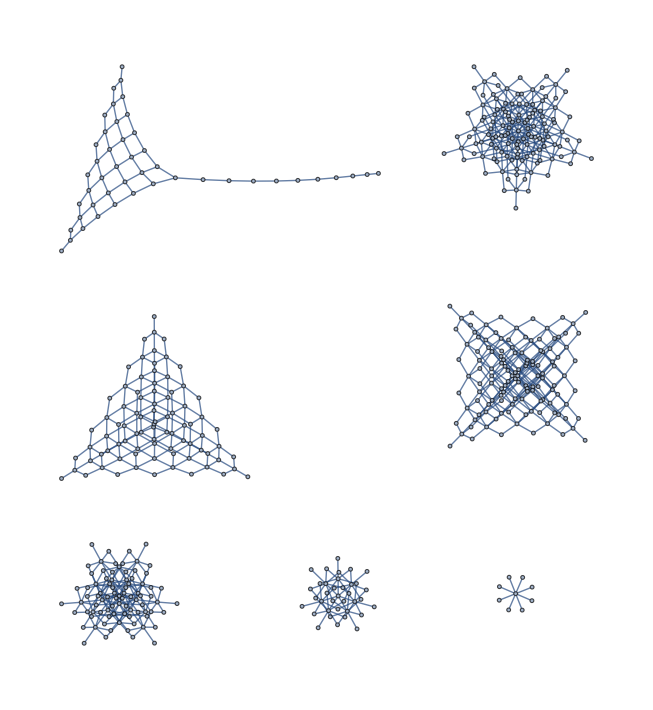

```mathematica
GraphPlot[Flatten[Table[Table[j->FromDigits[Insert[IntegerDigits[j,2],1,i],2],{i,Length[IntegerDigits[j,2]]+1}],{j,0,2^8-1}]],GraphLayout->{"EdgeLayout"->"StraightLine"}]
```

```mathematica
GraphPlot[Graph[{1 -> 2, 2 -> 4, 3 -> 1, 4-> 2, 2 -> 3, 3 -> 4}]]
```

-Graphics-

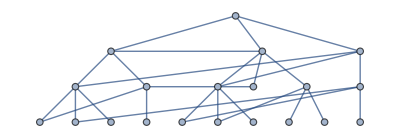

```mathematica
TreePlot[Flatten[Table[{i -> 2i + j -1}, {j, 3}, {i, 9}]]]
```

```mathematica
GraphPlot[Table[i -> Mod[i^3, 200], {i, 200}]]
```

-Graphics-

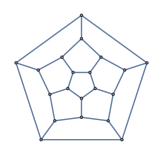

```mathematica
PolyhedronData["Dodecahedron", "Skeleton"]
```

```mathematica
PolyhedronData["Dodecahedron","Circumsphere"]
```

Sphere[{0,0,0},1/4 (√3+√15)]

```mathematica
PolyhedronData["Dodecahedron","SurfaceArea"]
```

3 √(5 (5+2 √5))

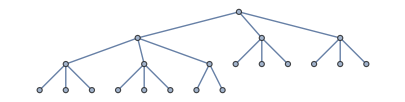

```mathematica
TreePlot[KaryTree[21, 3]]
```

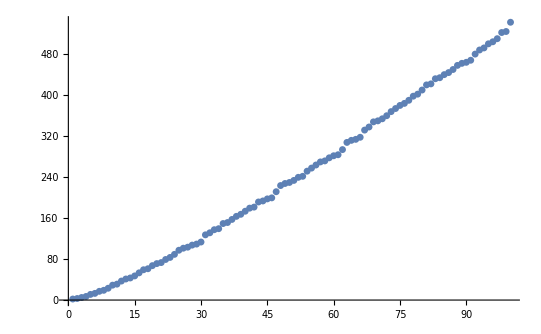

```mathematica
ListPlot[Prime[Range[100]]]
```

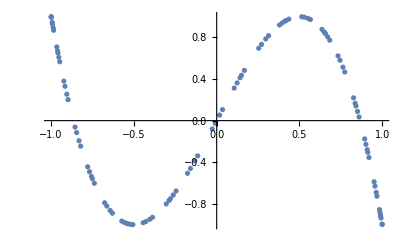

```mathematica
ListPlot[Table[{Sin[n], Sin[3n]}, {n, 100}]]
```

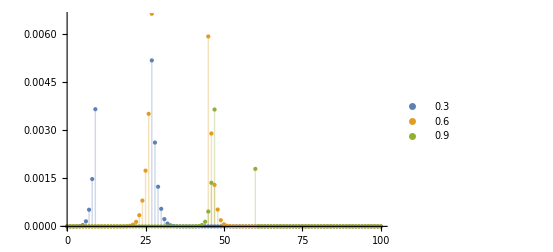

```mathematica
ListPlot[Table[{k, PDF[BinomialDistribution[60, p], k]}, {p, {0.3, 0.6, 0.9}}, {k, 0, 100}], Filling-> Axis, PlotLegends->{0.3, 0.6, 0.9}]
```

```mathematica
Laplacian[{f[x, y], g[x, y]}, {x, y}]
```

{f^(0,2)[x,y]+f^(2,0)[x,y],g^(0,2)[x,y]+g^(2,0)[x,y]}

```mathematica
{Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y],Derivative[0,2][g][x,y]+Derivative[2,0][g][x,y]}{x,y}
```

g^(0,3)[x,y]+f^(1,2)[x,y]+g^(2,1)[x,y]+f^(3,0)[x,y]

```mathematica
{Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y],Derivative[0,2][g][x,y]+Derivative[2,0][g][x,y]}{x,y}
```

-f^(0,3)[x,y]+g^(1,2)[x,y]-f^(2,1)[x,y]+g^(3,0)[x,y]

```mathematica
{Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y],Derivative[0,2][g][x,y]+Derivative[2,0][g][x,y]}{x,y}
```

{{f^(1,2)[x,y]+f^(3,0)[x,y],f^(0,3)[x,y]+f^(2,1)[x,y]},{g^(1,2)[x,y]+g^(3,0)[x,y],g^(0,3)[x,y]+g^(2,1)[x,y]}}

```mathematica
FourierTransform[Exp[-t^2]Cos[t], t, ω]
```

Cosh[1/4 (-1+ω)^2]/(2 √2)+Cosh[1/4 (1+ω)^2]/(2 √2)-Sinh[1/4 (-1+ω)^2]/(2 √2)-Sinh[1/4 (1+ω)^2]/(2 √2)

```mathematica
FourierTransform[HeavisideTheta[t], t, ω]
```

ⅈ/(√(2 π) ω)+√(π/2) DiracDelta[ω]

```mathematica
RandomPolyhedron[{"ConvexHull", 10}]
```

Polyhedron[…]

```mathematica
Region[%]
```

-Graphics3D-

```mathematica
ComplexPlot3D[JacobiEpsilon[z, 1/2], {z, 6}]
```

# -Graphics3D-

### Fundamentals of Science

- Break things down to the basic elements (primitives) 
- Evolve from these primitives, constantly stress test your models
- Make modifications: 
a better way to formulate your primitives; 
come up with some different rules.

```mathematica
Table[FromDigits[Reverse[IntegerDigits[n, 2, 7]], 2], {n, 0, 2^7 - 1}]
```

{0,64,32,96,16,80,48,112,8,72,40,104,24,88,56,120,4,68,36,100,20,84,52,116,12,76,44,108,28,92,60,124,2,66,34,98,18,82,50,114,10,74,42,106,26,90,58,122,6,70,38,102,22,86,54,118,14,78,46,110,30,94,62,126,1,65,33,97,17,81,49,113,9,73,41,105,25,89,57,121,5,69,37,101,21,85,53,117,13,77,45,109,29,93,61,125,3,67,35,99,19,83,51,115,11,75,43,107,27,91,59,123,7,71,39,103,23,87,55,119,15,79,47,111,31,95,63,127}

```mathematica
Table[{{"[◼]", "BranchialGraph"}}[ResourceFunction["NestGraphTagged"][n|->{Ceiling[5n/3],Ceiling[7n/5],Ceiling[11n/7]},1,t]],{t,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

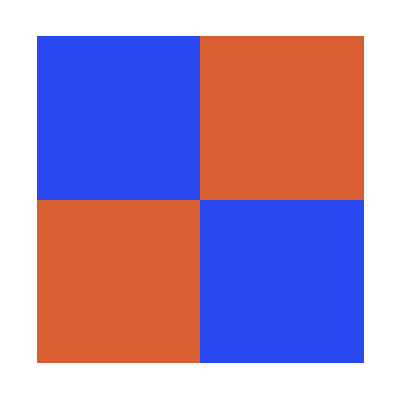
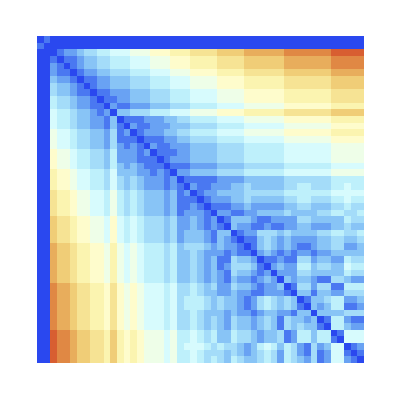
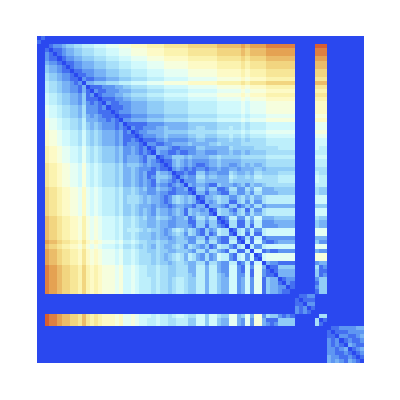
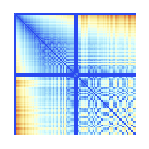
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[GraphDistanceMatrix[#]/.∞->0,ColorFunction->"LightTemperatureMap",ImageSize->.9->1.25]&/@Table[{{"[◼]", "BranchialGraph"}}[ResourceFunction["NestGraphTagged"][n|->{Ceiling[5n/3],Ceiling[7n/5],Ceiling[11n/7]},1,t]],{t,2,9}]
```

```mathematica
KirchhoffMatrix[%2]
```

SparseArray[…]

## Numerical Multicomputation

```mathematica
ResourceFunction["NestGraphTagged"][n|->{2n,4n},1,10,"StateLabeling"->True,"RuleStyling"->{RGBColor[0.1986453769853516, 0.33226123030078125, 0.9383540923955078],RGBColor[0.8489059725, 0.15, 0.19988236812499993]}]
```

-Graphics-

```mathematica
ArrayPlot[GraphDistanceMatrix[#]/.∞->0,ColorFunction->"LightTemperatureMap",PlotTheme->"Scientific",ImageSize-> Tiny]&/@Table[{{"[◼]", "BranchialGraph"}}[ResourceFunction["NestGraphTagged"][n|->{2n,4n},1,i]],{i,1,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Tally[%6]
```

{{-Graphics-,6}}

```mathematica
GraphDistanceMatrix[-Graphics-]//MatrixForm
```

(0 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2
2 | 0 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 0 | 2 | 1 | 2 | 2 | 1 | 2 | 2
1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2
2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1
1 | 2 | 2 | 2 | 2 | 0 | 1 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 0)

```mathematica
ArrayPlot[%8]
```

-Graphics-

```mathematica
Show[%10,ImageSize->Tiny]
```

-Graphics-

## Persona

All your resources, your personal setups, your computers, your data

I think you can setup some constraints: Learn from all the people that are alive; study from all the resources available on the Internet(with well defined purposes); 
Then, you can expand & evolve from these primitives.

# Programs

```mathematica
Plot3D[1/(x^3+y^2), {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
Quantity[1,"Newtons"]
```

1 N

```mathematica
N[2 Quantity[, "SpeedOfLight"]]
```

2. c

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Saving WolframLanguageData...

```mathematica
{{-Graphics-, QuantumBasis}}[2]
```

QuantumBasis[…]

```mathematica
PacletInstall/@{"CodeParser", "CodeFormatter"}
```

{PacletObject[…],PacletObject[…]}

```mathematica
s[x_][y_][z_]->x[z][y[z]];
k[x_][y_]->x;
```

```mathematica
s[s][s][s]
```

s[s][s][s]

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
ReverseApplied[f][a,b]
```

f[b,a]

```mathematica
Function[x,Function[y,2x+y]][a][b]
```

2 a+b

```mathematica
Plus[a,b,c]
```

a+b+c

```mathematica
Join[{a,b},{c,d,e}]
```

{a,b,c,d,e}

```mathematica
f[1]=1;
f[n_]:=n f[n-1];
```

```mathematica
f[4]
```

24

```mathematica
ResourceFunction["EnumerateCombinators"]
```

```mathematica
pf = FindEquationalProof[
  p·(q·(q·q)) == 
   p·p, ∀_{p,q,r}((p·q)·r)·(p·((p·r)·p))==r]
```

ProofObject[…]

```mathematica
pf["ProofNotebook"]
```

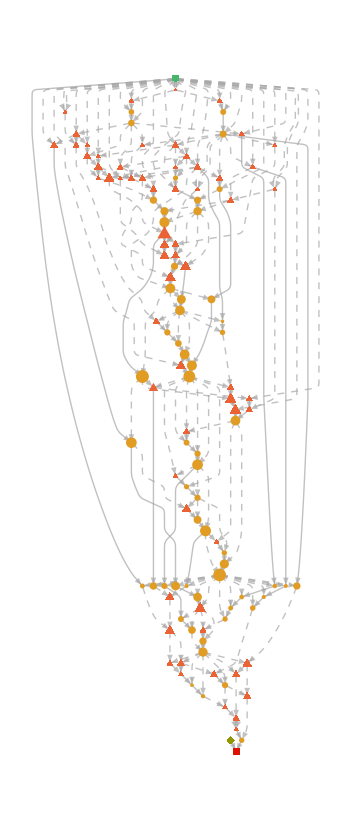

```mathematica
pf["ProofGraphWeighted"]
```

```mathematica
l=List[x,y,z]
```

{x,y,z}

```mathematica
l[[-1]]
```

z

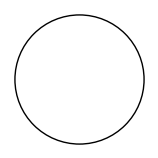

```mathematica
Graphics[Circle[{0,0}]]
```

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

```mathematica
Synonyms["present"]
```

{acquaint,award,confront,deliver,demo,demonstrate,exhibit,face,gift,give,introduce,lay out,nowadays,portray,pose,present tense,represent,salute,show,stage,submit}

```mathematica
sierpinski
```

-Graphics3D-

```mathematica
Export["sierpinski.stl",sierpinski]
```

sierpinski.stl

```mathematica
ARPublish[sierpinski]
```

ARPublish::os: ARPublish is not yet available on Windows.

ARPublish[sierpinski]

```mathematica
res = Parallelize[Map[PrimeQ[2^#-1]&, Range[9601,12000]]];
```